Warning: more than 31 qubits may cause errors - MMA uses ints to store array lengths

```mathematica
(* @TODO: package this? *)
```

```mathematica
(* disables gate (symbol and integer suscript) commutivity, replaces Times with Dot *)
$Pre = 
  Function[{arg}, 
   ReleaseHold[
    Hold[arg] //.  
     Times[α___, 
       patt : (Longest[(Subscript[_Symbol, _Integer]|Subscript[_Symbol, _Integer][___]) ..]), ω___] :> 
      Times[α, Dot[patt], ω]], HoldAll];

(* opcodes *)
getOpCode[gate_] :=
	gate /. {H->0,X->1,Y->2,Z->3,Rx->4,Ry->5,Rz->6,S->7,T->8}

(* recognising gates *)
gatePatterns = {
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ__Integer][arg_]] :> {getOpCode[gate], ctrl, targ, arg},
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ_Integer]] :> {getOpCode[gate], ctrl, targ, 0},
	Subscript[gate_Symbol, targ_Integer][arg_] :> {getOpCode[gate], -1, targ, arg},
	Subscript[gate_Symbol, targ_Integer] :> {getOpCode[gate], -1, targ, 0}
};

(* converting gate sequence to code lists: {opcodes, ctrls, targs, params} *)
codifyCircuit[circuit_Dot] :=
	circuit /. Dot -> List /. gatePatterns // Reverse // Transpose

(* applying a sequence of symoblic gates to a qureg *)
ApplyCircuit::usage = "ApplyCircuit[circuit, qureg] modifies qureg by applying the circuit.\nApplyCircuit[circuit, inQureg, outQureg] leaves inQureg unchanged, but modifies outQureg to be the result of applying the circuit to inQureg.";
ApplyCircuit[circuit_Dot, qureg_Integer] :=
	With[
		{codes = codifyCircuit[circuit]},
		If[
			AllTrue[ codes[[4]], NumericQ],
			ApplyCircuitInternal[qureg, codes[[1]], codes[[2]], codes[[3]], codes[[4]]],
			Echo["Some non-numerical arguments were passed to the backend!", "Error: "]; $Failed
		]
	]
(* apply a circuit to get an output state without changing input state *)
ApplyCircuit[circuit_Dot, inQureg_Integer, outQureg_Integer] :=
	Block[{},
		CloneQureg[outQureg, inQureg];
		ApplyCircuit[circuit, outQureg]
	]

(* destroying a remote qureg, and clearing the local symbol *)
SetAttributes[DestroyQureg, HoldAll];
DestroyQureg::usage = "DestroyQureg[qureg] destroys the qureg associated with the given ID or symbol.";
DestroyQureg[qureg_Integer] :=
	DestroyQuregInternal[qureg]
DestroyQureg[qureg_Symbol] :=
	Block[{}, DestroyQuregInternal[ReleaseHold@qureg]; Clear[qureg]]

GetMatrix::usage = "GetMatrix[qureg] returns the state-vector or density matrix associated with the given qureg.";
GetMatrix[qureg_Integer] :=
	With[{data = GetStateVecInternal[qureg]},
		Which[
			data === -1,
			$Failed,
			data[[2]] === 0,
			MapThread[#1 + ⅈ #2 &, {data[[3]], data[[4]]}],
			data[[2]] === 1,
			Transpose @ ArrayReshape[
				MapThread[#1 + ⅈ #2 &, {data[[3]], data[[4]]}], 
				{2^data[[1]],2^data[[1]]}]
		]
	]
	
SetMatrix::usage = "SetMatrix[qureg, matr] modifies qureg, overwriting its statevector or density matrix with that passed.";
SetMatrix[qureg_Integer, elems_List] :=
	With[{flatelems = 
		Which[
			(* vectors in various forms *)
			Length @ Dimensions @ elems === 1,
				elems,
			First @ Dimensions @ elems === 1,
				First @ elems,
			(Dimensions @ elems)[[2]] === 1,
				First @ Transpose @ elems,
			(* density matrices *)
			SquareMatrixQ @ elems,
				Flatten @ Transpose @ elems
		]},
		InitStateFromAmps[qureg, Re[flatelems], Im[flatelems]]
	]
```

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
Install["quest_link"];
```

## API

```mathematica
?CreateQureg
?CreateDensityQureg
?DestroyQureg
?DestroyAllQuregs
?GetAllQuregs
```

CreateQureg[numQubits] returns the id of a newly created remote statevector.

CreateDensityQureg[numQubits] returns the id of a newly created remote density matrix.

DestroyQureg[qureg] destroys the qureg associated with the given ID or symbol.

DestroyAllQuregs[] destroys all remote quregs.

GetAllQuregs[] returns all active quregs.

```mathematica
?InitZeroState
?InitPlusState
?InitClassicalState
?InitPureState
?InitStateFromAmps
?CloneQureg
?SetMatrix
```

InitZeroState[qureg] returns a state in |0>.

InitPlusState[qureg] returns a state in |+>.

InitClassicalState[qureg, ind] returns a state in basis state |ind>.

InitPureState[targetQureg, pureQureg] puts targetQureg (statevec or density matrix) into the pureQureg (statevec) state.

InitStateFromAmps[qureg, reals, imags] initialises the given qureg to have the supplied amplitudes.

CloneQureg[dest, source] sets dest to be a copy of source.

SetMatrix[qureg, matr] modifies qureg, overwriting its statevector or density matrix with that passed.

```mathematica
?ApplyCircuit
```

ApplyCircuit[circuit, qureg] modifies qureg by applying the circuit.
ApplyCircuit[circuit, inQureg, outQureg] leaves inQureg unchanged, but modifies outQureg to be the result of applying the circuit to inQureg.

```mathematica
?ApplyOneQubitDephaseError
?ApplyOneQubitDepolariseError
?ApplyTwoQubitDephaseError
?ApplyTwoQubitDepolariseError
```

ApplyOneQubitDephaseError[qureg, qubit, prob] adds dephasing noise to density matrix qureg.

ApplyOneQubitDepolariseError[qureg, qubit, prob] adds depolarising noise to density matrix qureg.

ApplyTwoQubitDephaseError[qureg, qb1, qb2 prob] adds dephasing noise to density matrix qureg.

ApplyTwoQubitDepolariseError[qureg, qb1, qb2 prob] adds depolarising noise to density matrix qureg.

```mathematica
?CalcProbOfOutcome
?CalcFidelity
?GetMatrix
```

CalcProbOfOutcome[qureg, qubit, outcome] returns the probability of measuring qubit in the given outcome.

CalcFidelity[qureg1, qureg2] returns the fidelity between the given states.

GetMatrix[qureg] returns the state-vector or density matrix associated with the given qureg.

## Demo

```mathematica
a = CreateDensityQureg @ 2;
InitPlusState @ a;
ApplyTwoQubitDepolariseError[a, 0, 1, .3];
ApplyTwoQubitDephaseError[a, 0, 1, .1];
MatrixForm @ GetMatrix @ a 
DestroyQureg @ a;
```

(0.25+0. ⅈ | 0.147333+0. ⅈ | 0.147333+0. ⅈ | 0.147333+0. ⅈ
0.147333+0. ⅈ | 0.25+0. ⅈ | 0.147333+0. ⅈ | 0.147333+0. ⅈ
0.147333+0. ⅈ | 0.147333+0. ⅈ | 0.25+0. ⅈ | 0.147333+0. ⅈ
0.147333+0. ⅈ | 0.147333+0. ⅈ | 0.147333+0. ⅈ | 0.25+0. ⅈ)

```mathematica
Install["quest_link"];

ψ = CreateQureg[20]

ApplyCircuit[Subscript[T, 3] Subscript[C, 0][Subscript[X, 1]], ψ]

DestroyQureg @ ψ;
```

0

0

Error:  the gate 'controlled Hadamard' is not supported. Aborting circuit and restoring qureg (id 1) to its original state.

Error:  the gate 'controlled Hadamard' is not supported. Aborting circuit and restoring qureg (id 1) to its original state.

Error:  the gate 'controlled Hadamard' is not supported. Aborting circuit and restoring qureg (id 1) to its original state.

«4 more identical outputs»

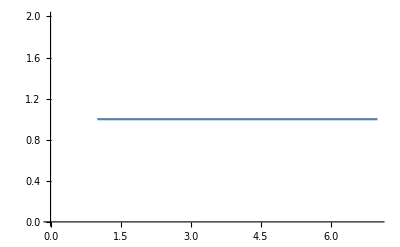

```mathematica
ψ = CreateQureg[20];
ϕ = CreateQureg[20];

InitPlusState[ψ];
InitPlusState[ϕ];

u[θ_] := Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[Ry, 3][θ] Subscript[H, 2] Subscript[X, 3] Subscript[T, 3] Subscript[C, 0][Subscript[H, 1]]

ListLinePlot @  Table[
	CalcFidelity[ψ, ApplyCircuit[u[θ],ψ,ϕ]],
	{θ, 0, 2π, 1}
]

DestroyQureg[ψ];
DestroyQureg[ϕ];
```

```mathematica
Uninstall["quest_link"];
```